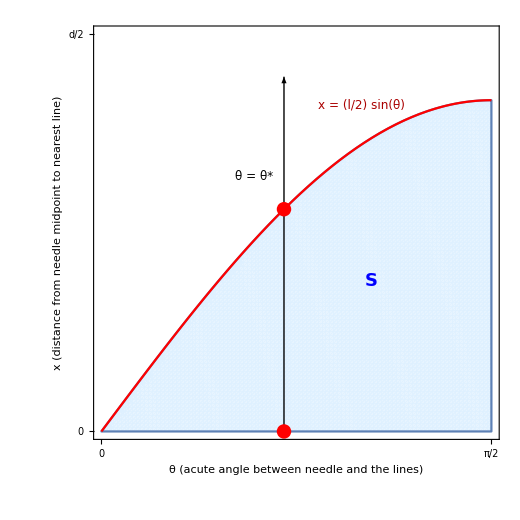

```mathematica
(*Parameters*)l=1;(*needle length*)d=1.2;(*line spacing,l<d*)θ0=Pi/4;(*chosen vertical slice angle*)(*Arrow x-position (slightly left of θ0)*)thetaArrow=θ0-0.05;

(*Upper dot y-coordinate on the curve at arrow θ*)
xTopArrow=(l/2) Sin[thetaArrow];

(*Region definition*)
region=ImplicitRegion[0≤θ≤Pi/2&&0≤x≤d/2&&x≤(l/2) Sin[θ],{θ,x}];

(*Plot region with arrow,dots,and labels*)
RegionPlot[Evaluate[RegionMember[region,{θ,x}]],{θ,0,Pi/2},{x,0,d/2},PlotPoints->100,Frame->True,Axes->False,PlotStyle->Directive[LightBlue,Opacity[0.7]],FrameLabel->{Style["θ (acute angle between needle and the lines)",14],Style["x (distance from needle midpoint to nearest line)",14]},(*Only ticks at 0 and π/2 (theta-axis) and 0,d/2 (x-axis)*)FrameTicks->{(*Left/right ticks (vertical x-axis)*){{{0,Style[0,12]},{d/2,Style["d/2",12]}},None},(*Bottom/top ticks (horizontal θ-axis)*){{{0,Style[0,12]},{Pi/2,Style["π/2",12]}},None}},Epilog->{(*Boundary curve:x=(l/2) sin(θ)*)Plot[(l/2) Sin[θ],{θ,0,Pi/2},PlotStyle->{Thick,Red}][[1]],(*Extended vertical arrow through region S*)Arrow[{{thetaArrow,0},{thetaArrow,xTopArrow+0.2}}],(*Dots at intersections with region boundary*){Red,PointSize[0.02],Point[{thetaArrow,0}],(*lower dot*)Point[{thetaArrow,xTopArrow}]},(*upper dot exactly on curve*)(*Label for region S moved up and right slightly*)Text[Style["S",18,Bold,Blue],{Pi/4+0.3,(l/2) Sin[Pi/4]/2+0.05}],(*Equation label for the curve,placed above it*)Text[Style["x = (l/2) sin(θ)",12,Darker@Red],{Pi/3,(l/2) Sin[Pi/3]+0.05},{0,-1}],(*Label for θ left of arrow*)Text[Style["θ = θ*",12,Black],{thetaArrow-0.12,xTopArrow+0.05}]},ImageSize->520,AspectRatio->1]
```